```mathematica
FunctE[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
FunctE1[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]

```mathematica
FunctE2[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
GammaSMLO[omega_,gammarx_,omegarx_]=gammarx*omega/omegarx
```

(gammarx omega)/omegarx

```mathematica
MainDirecroty=NotebookDirectory[]
```

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\

```mathematica
Filename="group_sn_fixed.dat";
DataExp=ReadList[FileNameJoin[{MainDirecroty,Filename}],Number];
Ncolumbs=3;
Nmaxpoints1=Length[DataExp]/Ncolumbs-1;
X1aver=Table[DataExp[[Ncolumbs*i+1]],{i,0,Nmaxpoints1}];
Y1aver=Table[DataExp[[Ncolumbs*i+2]],{i,0,Nmaxpoints1}];
dY1aver=Table[DataExp[[Ncolumbs*i+3]],{i,0,Nmaxpoints1}];
Clear[DataExp]
```

```mathematica
Needs["ErrorBarPlots`"]
```

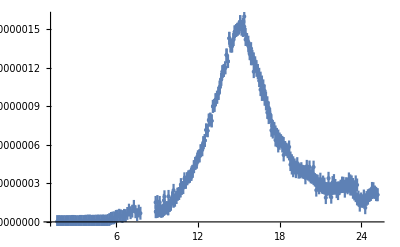

```mathematica
ErrorListPlot[{Transpose[{X1aver,Y1aver,dY1aver}]},PlotRange->All]
```

```mathematica
(* Fit  the cross section in the region [Ulow,Uupper] *)
```

```mathematica
Ulow=0.0;
Uupper=25.0;
Nlow=1;
Nupper=Length[Y1aver]
Do[If[X1aver[[i]]<Ulow,Nlow=i,Nlow=Nlow],{i,1,Length[Y1aver]}];
Do[If[X1aver[[i]]<Uupper,Nupper=i,Nupper=Nupper],{i,1,Length[Y1aver]}];
Nlow
Nupper
```

391

1

391

```mathematica
1
```

1

```mathematica
(*X1aver*)
```

```mathematica
(*Y1aver*)
```

```mathematica
(*dY1aver*)
```

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[0.-Im[(0.000117469+0. ⅈ)/(248.39+«1»-«1»+(7.04238 («5»)^2)/(100.+«1»-«1»))]]

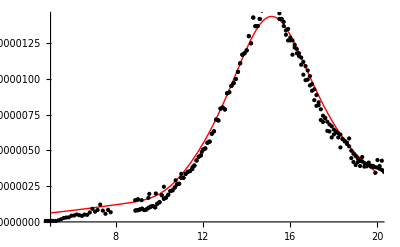

15.7604

10.

3.

1.4871

2.65375

0.0108383

0.

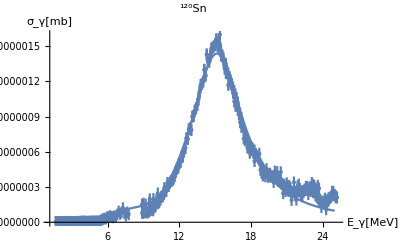

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-788.537] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-817.601] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.7604 | 0.104921 | 150.212 | 0.
omega2p | 10. | 0.719817 | 13.8924 | 7.78074×10^-36
Gamma1p | 3. | 0.290878 | 10.3136 | 3.53401×10^-22
Gamma2p | 1.4871 | 0.819009 | 1.81573 | 0.0701918
Gamma12p | 2.65375 | 0.42887 | 6.18777 | 1.56579×10^-9
Z10 | 0.0108383 | 0.0000668142 | 162.216 | 0.
Z20 | 0. | 0.000494267 | 0. | 1.

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-788.537] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-817.601] is too small to represent as a normalized machine number; precision may be lost.

{{15.7604,0.104921,150.212,0.},{10.,0.719817,13.8924,7.78074×10^-36},{3.,0.290878,10.3136,3.53401×10^-22},{1.4871,0.819009,1.81573,0.0701918},{2.65375,0.42887,6.18777,1.56579×10^-9},{0.0108383,0.0000668142,162.216,0.},{0.,0.000494267,0.,1.}}

1.7201

1.7201

```mathematica
(*TSE  !!!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,Nlow,Nmaxpointstemp}];
FordY1aver=Table[dY1aver[[i]],{i,Nlow,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p < 17, 7<omega2p<10, 3<Gamma1p<6, 1<Gamma2p<3, 0<Gamma12p<6 (*, Z10<10, Z20<10*)
},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","120"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[0.0000914924/(233.489+(0.+4.16958 ⅈ) omega-omega^2)+(9.99499×10^9)/(4.06432×10^11+(«1») «5»-omega^2)]]

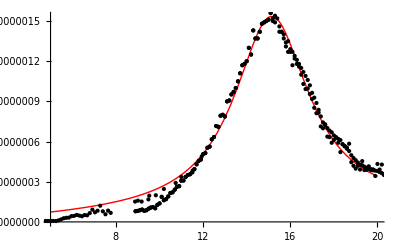

15.2803

637520.

4.16958

100001.

0.00956517

99975.

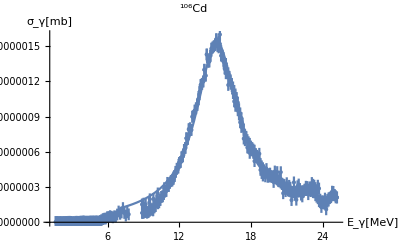

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1526.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1563.72] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-831.305] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.2803 | 0.0149028 | 1025.33 | 0.
omega2p | 637520. | 564.293 | 1129.77 | 0.
Gamma1p | 4.16958 | 0.0525887 | 79.2867 | 1.45038×10^-240
Gamma2p | 100001. | 899.36 | 111.191 | 1.03662×10^-294
Z10 | 0.00956517 | 0.0000571195 | 167.459 | 0.
Z20 | 99975. | 1799.19 | 55.5666 | 5.73218×10^-186

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1526.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1563.72] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-831.305] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{15.2803,0.0149028,1025.33,0.},{637520.,564.293,1129.77,0.},{4.16958,0.0525887,79.2867,1.45038×10^-240},{100001.,899.36,111.191,1.03662×10^-294},{0.00956517,0.0000571195,167.459,0.},{99975.,1799.19,55.5666,5.73218×10^-186}}

1.23074

1.23074

```mathematica
(*independent Gamma12p=0 !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0, 10<omega1p < 20 },{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam0[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam0=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(5.54654×10^7+((0.+«21» ⅈ) omega)/(235.706+«1»-«1»))/(«4»+(1.00575×10^-9 «1»)/(235.706+«1»-«1»))+(«21»+(«1»)/(«1»))/(«18»+«1»«1»«1»+(«1»)/(«1»))]]

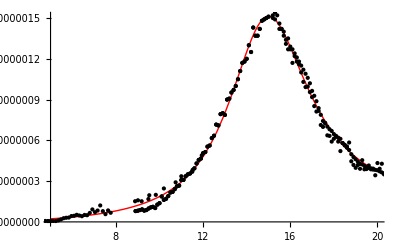

15.3527

32365.6

4.79417

97539.7

0.0000317136

0.010306

7447.51

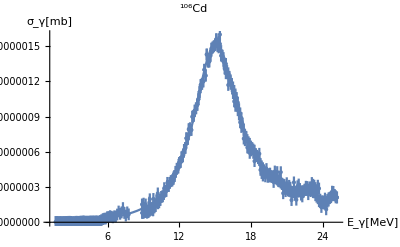

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1193.23] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1091.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2555.62] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.3527 | 0.0353647 | 434.126 | 0.
omega2p | 32365.6 | 97.3553 | 332.448 | 0.
Gamma1p | 4.79417 | 0.630161 | 7.60785 | 2.1727×10^-13
Gamma2p | 97539.7 | 6.46087 | 15097. | 0.
Gamma12p | 0.0000317136 | 0.563741 | 0.0000562556 | 0.999955
Z10 | 0.010306 | 0.0000674055 | 152.895 | 0.
Z20 | 7447.51 | 169.236 | 44.0068 | 4.41664×10^-152

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1193.23] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1091.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2555.62] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{15.3527,0.0353647,434.126,0.},{32365.6,97.3553,332.448,0.},{4.79417,0.630161,7.60785,2.1727×10^-13},{97539.7,6.46087,15097.,0.},{0.0000317136,0.563741,0.0000562556,0.999955},{0.010306,0.0000674055,152.895,0.},{7447.51,169.236,44.0068,4.41664×10^-152}}

0.525275

0.525275

```mathematica
(*TSE SMLO GDR and PDR *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(1.09039×10^-15+((0.+«23» ⅈ) omega)/(540.79+«1»«1»«1»))/(0.0661401+«1»-«1»+(905.816 («5»)^2)/(540.79+«1»-«1»))+(«1»)/(«1»)]]

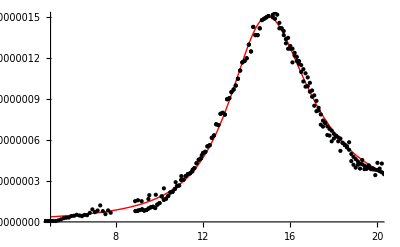

0.257177

23.2549

-0.13977

8.91855

30.0968

3.30211×10^-8

0.0158969

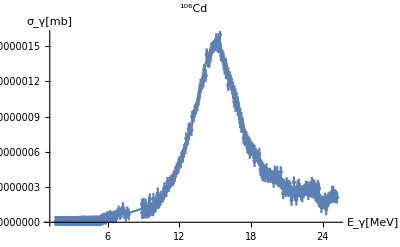

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 0.257177 | 699.384 | 0.000367719 | 0.999707
omega2p | 23.2549 | 9.87612 | 2.35466 | 0.0190424
Gamma1p | -0.13977 | 379.871 | -0.00036794 | 0.999707
Gamma2p | 8.91855 | 40.6729 | 0.219275 | 0.826552
Gamma12p | 30.0968 | 59.9523 | 0.502012 | 0.615947
Z10 | 3.30211×10^-8 | 0.0107496 | 3.07185×10^-6 | 0.999998
Z20 | 0.0158969 | 0.0103416 | 1.53717 | 0.125074

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{0.257177,699.384,0.000367719,0.999707},{23.2549,9.87612,2.35466,0.0190424},{-0.13977,379.871,-0.00036794,0.999707},{8.91855,40.6729,0.219275,0.826552},{30.0968,59.9523,0.502012,0.615947},{3.30211×10^-8,0.0107496,3.07185×10^-6,0.999998},{0.0158969,0.0103416,1.53717,0.125074}}

0.639072

0.639072

```mathematica
(*TSE SMLO GDR and PDG G=const !!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-Im[(138.164+((0.+«18» ⅈ) omega)/(224.043+«1»-«1»))/(1.25478×10^7-«1»«1»«1»+(3630.84 («5»)^2)/(224.043+«1»«1»«1»))+(«1»«1»«1»)/(«1»)]]

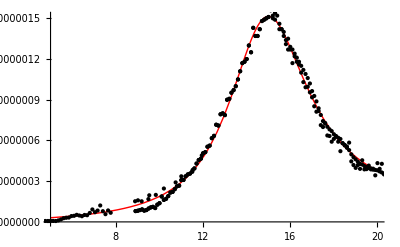

14.9681

3542.29

-55.7862

454424.

60.2565

0.0100113

11.7543

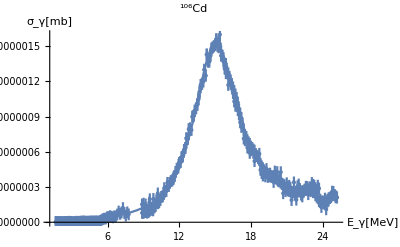

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-836.622] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 14.9681 | 0.477007 | 31.3791 | 5.05825×10^-108
omega2p | 3542.29 | 268605. | 0.0131877 | 0.989485
Gamma1p | -55.7862 | 2250.17 | -0.0247919 | 0.980234
Gamma2p | 454424. | 2664.14 | 170.57 | 0.
Gamma12p | 60.2565 | 2249.92 | 0.0267816 | 0.978648
Z10 | 0.0100113 | 0.000707219 | 14.1559 | 6.67712×10^-37
Z20 | 11.7543 | 2225.13 | 0.00528254 | 0.995788

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-836.622] is too small to represent as a normalized machine number; precision may be lost.

{{14.9681,0.477007,31.3791,5.05825×10^-108},{3542.29,268605.,0.0131877,0.989485},{-55.7862,2250.17,-0.0247919,0.980234},{454424.,2664.14,170.57,0.},{60.2565,2249.92,0.0267816,0.978648},{0.0100113,0.000707219,14.1559,6.67712×10^-37},{11.7543,2225.13,0.00528254,0.995788}}

0.552512

0.552512

```mathematica
(*TSE SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[0.000106231/(235.709-(1.-0.312303 ⅈ) omega^2)+3.31917/(236854.-(1.-«18» ⅈ) («5»)^2)]]

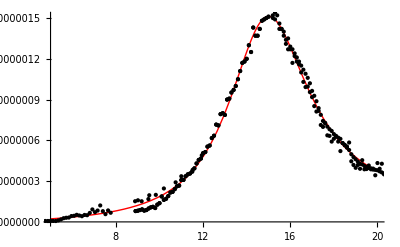

15.3528

486.677

4.79472

1246.97

0.0103068

1.82186

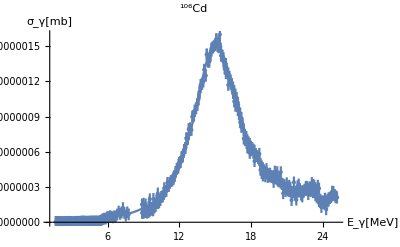

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1521.37] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.3528 | 0.0151703 | 1012.03 | 0.
omega2p | 486.677 | 70102.1 | 0.0069424 | 0.994464
Gamma1p | 4.79472 | 0.0705864 | 67.927 | 1.95457×10^-216
Gamma2p | 1246.97 | 1.22723×10^7 | 0.000101608 | 0.999919
Z10 | 0.0103068 | 0.000100188 | 102.875 | 3.90311×10^-282
Z20 | 1.82186 | 9588.49 | 0.000190005 | 0.999848

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1521.37] is too small to represent as a normalized machine number; precision may be lost.

{{15.3528,0.0151703,1012.03,0.},{486.677,70102.1,0.0069424,0.994464},{4.79472,0.0705864,67.927,1.95457×10^-216},{1246.97,1.22723×10^7,0.000101608,0.999919},{0.0103068,0.000100188,102.875,3.90311×10^-282},{1.82186,9588.49,0.000190005,0.999848}}

0.523812

0.523812

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[12.9265/(2.84817×10^6+(0.+2200.91 ⅈ) omega-omega^2)+0.000103302/(235.714-(1.-«19» ⅈ) «1»)]]

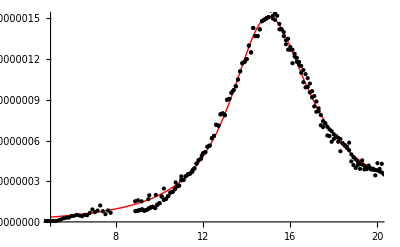

15.353

1687.65

4.70717

2200.91

0.0101638

3.59534

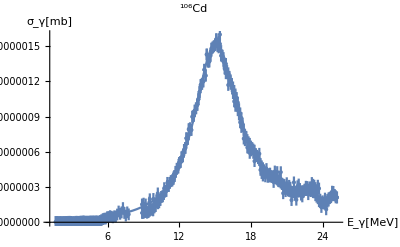

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1586.47] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-751.89] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.353 | 0.0128096 | 1198.55 | 0.
omega2p | 1687.65 | 3.75671×10^8 | 4.49237×10^-6 | 0.999996
Gamma1p | 4.70717 | 0.0593973 | 79.2489 | 1.72399×10^-240
Gamma2p | 2200.91 | 4.03867×10^8 | 5.4496×10^-6 | 0.999996
Z10 | 0.0101638 | 0.0000748609 | 135.769 | 0.
Z20 | 3.59534 | 1.27077×10^6 | 2.82926×10^-6 | 0.999998

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1586.47] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-751.89] is too small to represent as a normalized machine number; precision may be lost.

{{15.353,0.0128096,1198.55,0.},{1687.65,3.75671×10^8,4.49237×10^-6,0.999996},{4.70717,0.0593973,79.2489,1.72399×10^-240},{2200.91,4.03867×10^8,5.4496×10^-6,0.999996},{0.0101638,0.0000748609,135.769,0.},{3.59534,1.27077×10^6,2.82926×10^-6,0.999998}}

0.578808

0.578808

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG G=const !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[0.0000954958/(233.175+(0.+4.28604 ⅈ) omega-omega^2)+(9.99774×10^9)/(6.65826×10^9-(1.-«1») «1»)]]

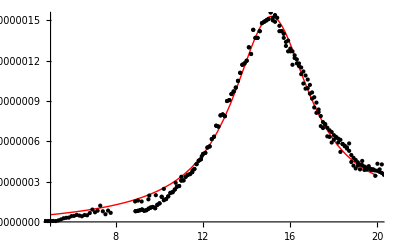

15.2701

81598.1

4.28604

99990.9

0.00977219

99988.7

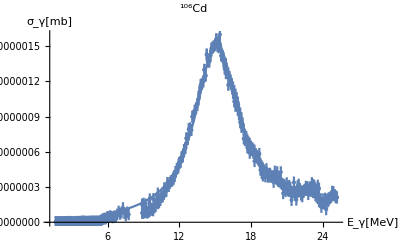

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1578.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-783.099] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1555.94] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.2701 | 0.0130152 | 1173.25 | 0.
omega2p | 81598.1 | 553.349 | 147.462 | 0.
Gamma1p | 4.28604 | 0.0415436 | 103.17 | 1.34842×10^-282
Gamma2p | 99990.9 | 90.3127 | 1107.16 | 0.
Z10 | 0.00977219 | 0.0000407267 | 239.945 | 0.
Z20 | 99988.7 | 180.629 | 553.558 | 0.

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1578.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-783.099] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1555.94] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{15.2701,0.0130152,1173.25,0.},{81598.1,553.349,147.462,0.},{4.28604,0.0415436,103.17,1.34842×10^-282},{99990.9,90.3127,1107.16,0.},{0.00977219,0.0000407267,239.945,0.},{99988.7,180.629,553.558,0.}}

0.934112

0.934112

```mathematica
(*independent Gamma12p=0, SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

```mathematica
"E:\\Sasha\\work\\Students\\Kucher\\Cd106\\FigSigmaFit106Cd.eps"
```

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

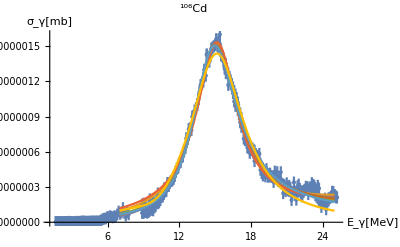

```mathematica
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[{ResponseFuncPDRsmloGDRsmlo[x],ResponseFuncPDRsmloGDRcons[x],ResponseFuncPDRconsGDRsmlo[x],ResponseFuncTSEgam0[x],ResponseFuncTSEPDRsmloGDRsmlo[x],ResponseFuncTSEPDRsmloGDRcons[x],ResponseFuncTSEPDRconsGDRsmlo[x],ResponseFuncTSEgam[x]},{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
```

```mathematica
Chi2PDRsmloGDRsmlo
Chi2PDRsmloGDRcons
Chi2PDRconsGDRsmlo
Chi2TSEgam0
Chi2TSEPDRsmloGDRsmlo
Chi2TSEPDRsmloGDRcons
Chi2TSEPDRconsGDRsmlo
Chi2TSEgam
```

0.523812

0.934112

0.578808

1.23074

0.525275

0.552512

0.639072

1.7201